```mathematica
Q2ind[x_]:=1/x;
Q2Eq2[Qvol_,CVx_,x_]:=(1-Qvol^2)/x+Qvol^2*(CVx^2+1);
Q2Eq4[x_,CVx_,v_,CVv_]:=1/x+((1+CVx^2)*(1+CVv^2))/v;
Q2Eq5[x_,s_,q_]:=(1+s)/x+(s*(q-1))/x^2;
optGen = {Frame->True,PlotStyle->AbsoluteThickness[3],FrameStyle->Directive[Black,Thick],RotateLabel->False,LabelStyle->Directive[35,FontFamily->"Palatino Linotype",Black]}; 
imSize = {ImageSize->600};
```

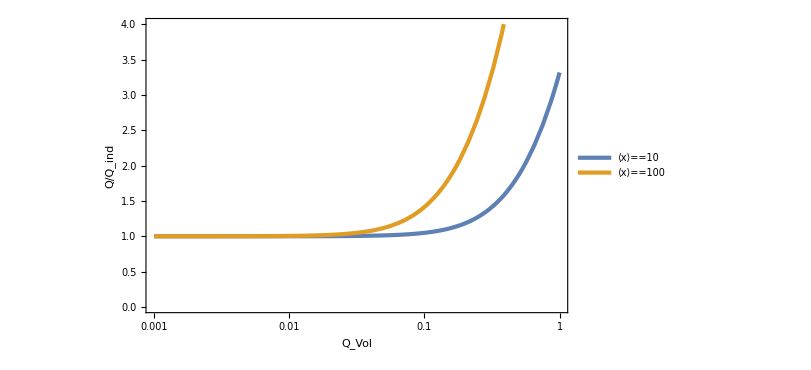

```mathematica
optLab2=FrameLabel->{Text[Style[ToExpression["Q_{Vol}",TeXForm,HoldForm]]],Text[Style[ToExpression["Q/Q_{ind}",TeXForm,HoldForm]]]};
legend2={PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["\\langle x\\rangle=10",TeXForm,HoldForm]]],Text[Style[ToExpression["\\langle x\\rangle=100",TeXForm,HoldForm]]]},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",2},Spacings->0.1],{0.2,0.82}]};
Show[LogLinearPlot[{Sqrt[Q2Eq2[Qvol,1/(√10),10]/Q2ind[10]],Sqrt[Q2Eq2[Qvol,1/(√100),100]/Q2ind[100]]},{Qvol,10^-3,1},PlotRange->{{10^-3,1},{0,4}},Evaluate[optGen],Evaluate[optLab2],Evaluate[legend2]],Evaluate[imSize]]
```

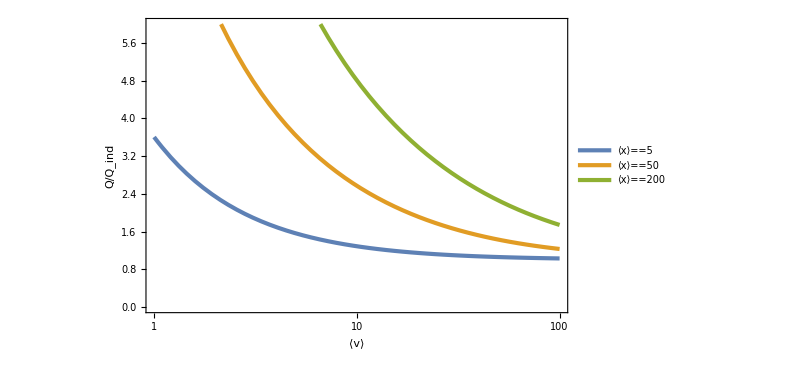

```mathematica
optLab4=FrameLabel->{Text[Style[ToExpression["\\langle v\\rangle",TeXForm,HoldForm]]],Text[Style[ToExpression["Q/Q_{ind}",TeXForm,HoldForm]]]};
legend4={PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["\\langle x\\rangle=5",TeXForm,HoldForm]]],Text[Style[ToExpression["\\langle x\\rangle=50",TeXForm,HoldForm]]],Text[Style[ToExpression["\\langle x\\rangle=200",TeXForm,HoldForm]]]},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",3},Spacings->0.01],{0.83,0.79}]};
Show[LogLinearPlot[{Sqrt[Q2Eq4[5,1/(√5),v,1/(√v)]/Q2ind[5]],Sqrt[Q2Eq4[50,1/(√50),v,1/(√v)]/Q2ind[50]],Sqrt[Q2Eq4[200,1/(√200),v,1/(√v)]/Q2ind[200]]},{v,1,10^2},PlotRange->{{1,10^2},{0,6}},Evaluate[optGen],Evaluate[optLab4],Evaluate[legend4]],Evaluate[imSize]]
```

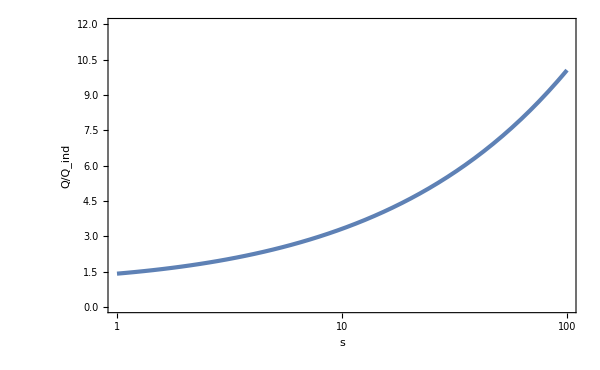

```mathematica
optLab5=FrameLabel->{Text[Style[ToExpression["s",TeXForm,HoldForm]]],Text[Style[ToExpression["Q/Q_{ind}",TeXForm,HoldForm]]]};
Show[LogLinearPlot[{Sqrt[Q2Eq5[5,s,1]/Q2ind[5]]},{s,1,10^2},PlotRange->{{1,10^2},{0,12}},Evaluate[optGen],Evaluate[optLab5]],Evaluate[imSize]]
(*Show[LogLinearPlot[{Sqrt[Q2Eq5[5,s,1]/Q2ind[5]],Sqrt[Q2Eq5[50,s,1]/Q2ind[50]],Sqrt[Q2Eq5[200,s,1]/Q2ind[200]]},{s,1,10^2},PlotRange->{{1,10^2},{0,12}},Evaluate[optGen],Evaluate[optLab5]],Evaluate[imSize]]*)
```

```mathematica
Q2Eq6[x_,K_,CVx_]:=1/x*(1-K*x*(CVx^2+1));
Q2Eq6a[K_,Kx_,CVx_]:=K/Kx*(1-Kx*(CVx^2+1));
P[x_,v_]:=1;
Q2Eq7[xAve_,Q2v_,sup_]:=1/xAve*(1-1/xAve*∑_(v=1)^sup ((1/v-Q2v)*∑_(x=0)^v (x^2*P[x,v])+(v-v^2*Q2v)*∑_(x=v+1)^sup P[x,v]));
Q2Eq8[x_,p_,k_]:=(1-(2*p-1)*k)/x;
```

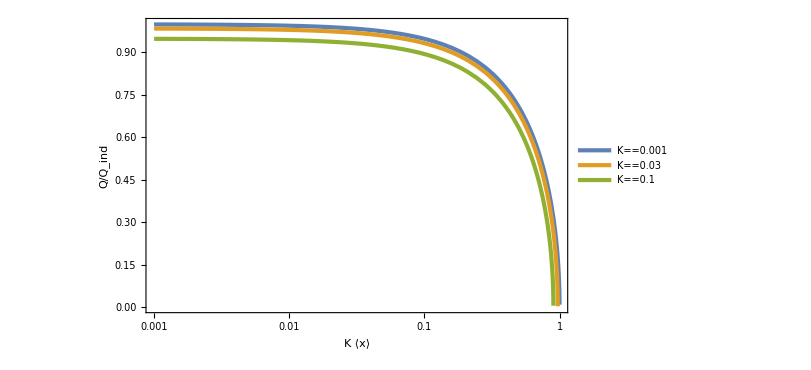

```mathematica
optLab6=FrameLabel->{Text[Style[ToExpression["K\\langle x\\rangle",TeXForm,HoldForm]]],Text[Style[ToExpression["Q/Q_{ind}",TeXForm,HoldForm]]]};
legend6={PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["K=0.001",TeXForm,HoldForm]]],Text[Style[ToExpression["K=0.03",TeXForm,HoldForm]]],Text[Style[ToExpression["K=0.1",TeXForm,HoldForm]]]},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",3},Spacings->0.01],{0.17,0.2}]};
Show[LogLinearPlot[{Sqrt[Q2Eq6a[0.001,Kx,1/(√(Kx/0.001))]/Q2ind[Kx/0.001]],Sqrt[Q2Eq6a[0.03,Kx,1/(√(Kx/0.03))]/Q2ind[Kx/0.03]],Sqrt[Q2Eq6a[0.1,Kx,1/(√(Kx/0.1))]/Q2ind[Kx/0.1]]},{Kx,10^-3,1},PlotRange->{{10^-3,1},{0,1}},Evaluate[optGen],Evaluate[optLab6],Evaluate[legend6]],Evaluate[imSize]]
```

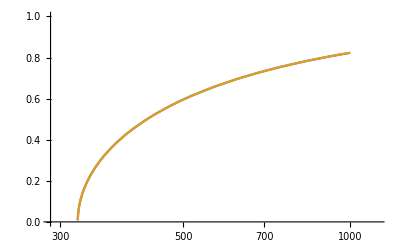

```mathematica
LogLinearPlot[{Sqrt[Q2Eq7[x,0,10]/Q2ind[x]],Sqrt[Q2Eq7[x,0,10]/Q2ind[x]]},{x,10^1,10^3},PlotRange->{0,1}]
```

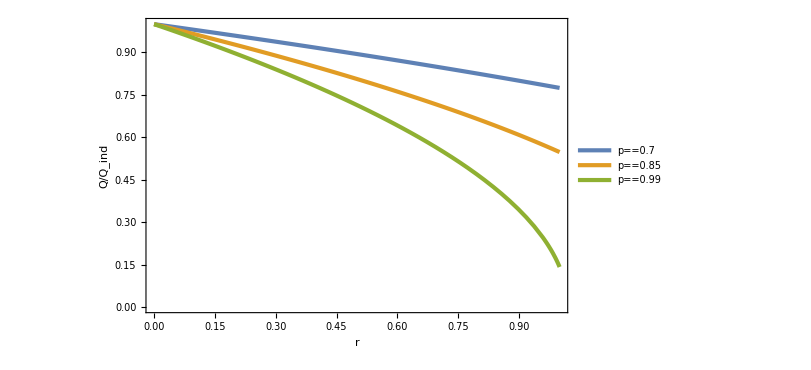

```mathematica
optLab8=FrameLabel->{Text[Style[ToExpression["r",TeXForm,HoldForm]]],Text[Style[ToExpression["Q/Q_{ind}",TeXForm,HoldForm]]]};
legend8={PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["p=0.7",TeXForm,HoldForm]]],Text[Style[ToExpression["p=0.85",TeXForm,HoldForm]]],Text[Style[ToExpression["p=0.99",TeXForm,HoldForm]]]},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",3},Spacings->0.01],{0.17,0.2}]};
Show[Plot[{Sqrt[Q2Eq8[10,0.7,k]/Q2ind[10]],Sqrt[Q2Eq8[10,0.85,k]/Q2ind[10]],Sqrt[Q2Eq8[10,0.99,k]/Q2ind[10]]},{k,0,1},Evaluate[optGen],Evaluate[optLab8],Evaluate[legend8],PlotRange->{{0,1},{0,1}}],Evaluate[imSize]]
```